```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/Users/zack/Documents/oscillators/faraday

## Single run plots

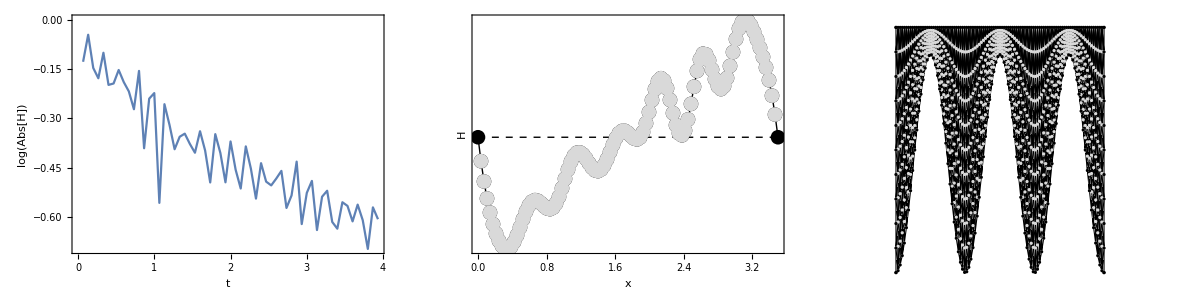

24.000000 0.500000 1.875000 -5.621843 1.795196 0.400000 0.000000

```mathematica
filebase="data/periodic";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
Grid[{{ListPlot[Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{{0,0},{length,0}}},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[m,All,2]]]-Min[mesh[[m,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[m,All,2]]],Max[mesh[[m,All,2]]]}}]}}]
lst[[-1]]
```

## Fig 3

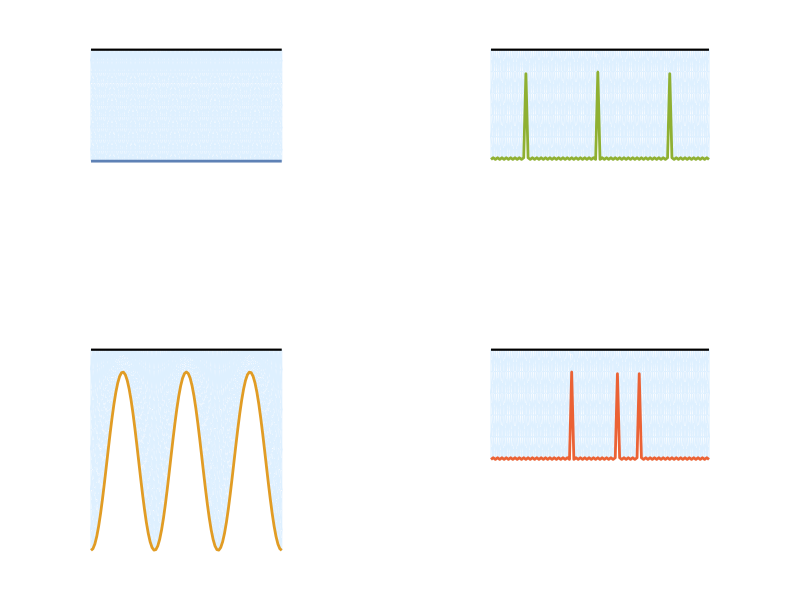

```mathematica
height=0.5;
length=4;
cols={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]};
filebases={"data/flat","data/periodic","data/sharp502","data/sharp574"};
p0=Grid@Transpose@Partition[Table[filebase=filebases[[i]];
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], Joined->True,ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.1)/(length+2),PlotRange->{{-1,length+1},{-0.5,0.6}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[cols[[i]],AbsoluteThickness[2]]},PlotRange->All]],{i,1,Length[filebases]}],2]
```

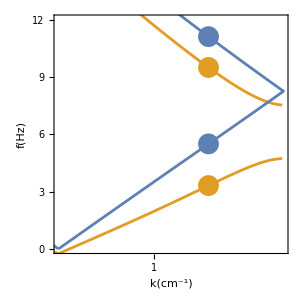

```mathematica
height=0.5;
length=4.0;
gap=2*Pi/length*3/2;
ks=2*gap;
hs=0.45;
M2=3;
κ[k_, n_]:=k+n*ks;
ν1=2;
ν3=0.1;
g=980;
σ=72;
ρ=1;
H1[k_,A_]:=Table[Exp[-κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*height]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*height]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*height]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
p1=Show[Show[ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,2*Pi/length,6*Pi/length,2*Pi/length}]],Joined->False,Axes->False,Frame->True,LabelStyle->Directive[16],PlotRange->{{-gap,gap},{0,12}},FrameTicks->{{Table[{i,i},{i,0,12,3}],Table[{i,""},{i,0,12,3}]},{Table[{i,i},{i,-3,3,1}],Table[{i,""},{i,-3,3,1}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotStyle->Directive[PointSize[0.05],ColorData[97,"ColorList"][[2]]]],ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,-2*Pi/length,-6*Pi/length,-2*Pi/length}]],Joined->False,PlotStyle->Directive[PointSize[0.05],ColorData[97,"ColorList"][[2]]]],ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,-ks/2+0.01,ks/2-0.01,ks/200}]],Joined->True,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]]],Show[ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,2*Pi/length,6*Pi/length,2*Pi/length}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,2*Pi/length,6*Pi/length,2*Pi/length}]},Joined->False,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.05]]],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]]]],PlotRange->{{0,gap},{0,12}}]
```

{3.9584,Null}

{0.323924,Null}

{4.03937,Null}

{0.317863,Null}

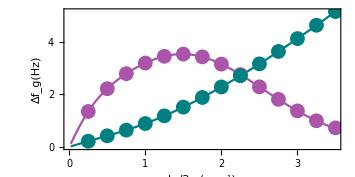

```mathematica
length=4;
M2=3;
ks0=Pi/25;
ks1=7*Pi;
dks=Pi/25;
AbsoluteTiming[gaps1=Table[{ks/(2*Pi),(#[[2]]-#[[1]])&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,ks0,ks1,dks}];]
AbsoluteTiming[gaps2=Table[{ks/(2*Pi),(#[[2]]-#[[1]])&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,2*Pi/length,ks1,2*Pi/length}];]
AbsoluteTiming[gaps3=Table[{ks/(2*Pi),((#[[2]]+#[[1]])/2)&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,ks0,ks1,dks}];]
AbsoluteTiming[gaps4=Table[{ks/(2*Pi),((#[[2]]+#[[1]])/2)&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,2*Pi/length,ks1,2*Pi/length}];]

scale1=5;
scale2=50;
p4=Show[ListPlot[{{#[[1]],#[[2]]/scale1}&/@gaps1,{#[[1]],#[[2]]/scale2}&/@gaps3},Axes->False,Frame->True,FrameLabel->{{Style[DisplayForm[RowBox[{Subscript[Δf,"g"], "(Hz)"}]],Lighter[Purple]],Style[DisplayForm[RowBox[{OverBar[Subscript[f,"g"]], "(Hz)"}]],RGBColor[{0,1/2,1/2}]]},{DisplayForm[RowBox[{Subscript[k,s],"/",2*Pi,"(",Superscript["cm",-1],")"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotStyle->{Directive[Lighter[Purple]],Directive[RGBColor[{0,1/2,1/2}]]},ImageSize->300,FrameTicks->{{Table[{i/scale1,Style[PaddedForm[i,{2,1}],Lighter[Purple]]},{i,0,scale1,scale1/5}],Table[{i/scale2,Style[i,RGBColor[{0,1/2,1/2}]]},{i,0,scale2,scale2/5}]},{Table[{i,i},{i,0,ks1/(2*Pi),1}],Table[{i,""},{i,0,3,0.5}]}}],ListPlot[{{#[[1]],#[[2]]/scale1}&/@gaps2,{#[[1]],#[[2]]/scale2}&/@gaps4},Joined->False,PlotStyle->{Directive[PointSize[0.03],Lighter[Purple]],Directive[PointSize[0.03],RGBColor[{0,1/2,1/2}]]}],ImageSize->355,ImagePadding->{{65,65},{65,10}},AspectRatio->1/2]
```

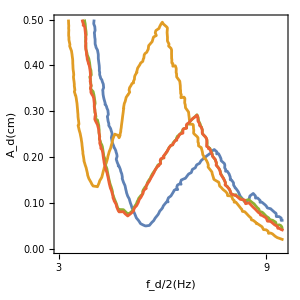

```mathematica
filebases={"sweeps/sharpamp/1001","sweeps/sharpamp/1003","sweeps/sharpamp/1002","sweeps/sharpamp/574"};
cols={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.5},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}]
```

```mathematica
ν1=2.0;
ν2=0.1;
g=980;
σ=72;
ρ=1;
length=4;
ks=(3 π)/2;
ω1=2*Pi*6;
ω2=2*Pi*20;
dω=2*Pi*0.05;
kmin=0;
kmax=ks;
height=0.5;
As=0.4;
M2=3;
M3=3;
mat1[s_,k_,ω_,As_,ks_,height_]:=ArrayFlatten[Table[Exp[-(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*((-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+(k+n*ks)^2*ν2))-(g+σ/ρ*(k+n*ks)^2)*(k+n*ks))*KroneckerDelta[m,o]*(BesselJ[n-l,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l-1,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l+1,I*(k+n*ks)*As])+Exp[(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*(-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+(k+n*ks)^2*ν2)+(g+σ/ρ*(k+n*ks)^2)*(k+n*ks))*KroneckerDelta[m,o]*(BesselJ[n-l,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l-1,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l+1,-I*(k+n*ks)*As]),{n,-M2,M2},{l,-M2,M2},{m,-M3,M3},{o,-M3,M3}]];
mat2[s_,k_,ω_,As_,ks_,height_]:=ArrayFlatten[Table[Exp[-(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*(ω^2*(k+n*ks)/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1])*(BesselJ[n-l,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l-1,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l+1,I*(k+n*ks)*As])+Exp[(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*(-ω^2*(k+n*ks)/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1])*(BesselJ[n-l,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l-1,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l+1,-I*(k+n*ks)*As]),{n,-M2,M2},{l,-M2,M2},{m,-M3,M3},{o,-M3,M3}]]
mat3[s_,k_,ω_,height_]:=ArrayFlatten[Table[((-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+k^2*ν2))+Tanh[k*height]*(g+σ/ρ*k^2)*k)*KroneckerDelta[m,o],{m,-M3,M3},{o,-M3,M3}]];
mat4[s_,k_,ω_,height_]:=ArrayFlatten[Table[-Tanh[k*height]*(ω^2*k/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1]),{m,-M3,M3},{o,-M3,M3}]]
AbsoluteTiming[vals5=DeleteCases[ParallelTable[val1=Abs[Cases[Eigenvalues[{mat1[0.0,2*Pi/length,ω,As,ks, height],mat2[0.0,2*Pi/length,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-2]];val2=Abs[Cases[Eigenvalues[{mat1[0.5,2*Pi/length,ω,As,ks,height],mat2[0.0,2*Pi/length,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-2]];
val=Join[val1,val2];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
AbsoluteTiming[vals1=DeleteCases[ParallelTable[val1=Abs[Cases[Eigenvalues[{mat3[0.5,2*Pi/length,ω, height],mat4[0.5,2*Pi/length,ω, height]}],u_/;Abs[Im[u]]<10^-6]];
val2=Abs[Cases[Eigenvalues[{mat3[0.5,2*Pi/length*2,ω, height],mat4[0.5,2*Pi/length*2,ω, height]}],u_/;Abs[Im[u]]<10^-6]];val3=Abs[Cases[Eigenvalues[{mat3[0.0,2*Pi/length*3,ω,height],mat4[0.0,2*Pi/length*3,ω,height]}],u_/;Abs[Im[u]]<10^-6]];
val=Join[val1,val2,val3];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
Export["data/periodicfloquet.txt",First@MinimalBy[#,#[[2]]&]&/@vals5,"Table"]
Export["data/flatfloquet.txt",First@MinimalBy[#,#[[2]]&]&/@vals1,"Table"]
```

{228.646,Null}

{0.33175,Null}

data/periodicfloquet.txt

data/flatfloquet.txt

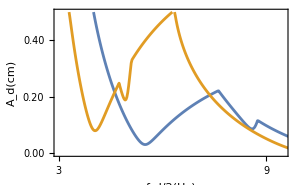

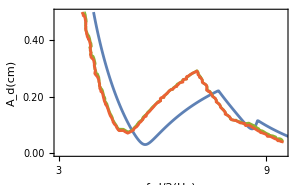

```mathematica
filebases={"sweeps/sharpamp/1002","sweeps/sharpamp/574"};
flatfloquet=Import["data/flatfloquet.txt","Table"];
periodicfloquet=Import["data/periodicfloquet.txt","Table"];
cols={ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Show[ListPlot[{flatfloquet,periodicfloquet},PlotRange->{{3,9.5},{0,0.5}},LabelStyle->Directive[16,Black], Joined->True,Axes->False,Frame->True,PlotStyle->Directive[AbsoluteThickness[2]],FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}]]
p3=Show[ListPlot[{flatfloquet},PlotRange->{{3,9.5},{0,0.5}},LabelStyle->Directive[16,Black], Joined->True,Axes->False,Frame->True,PlotStyle->Directive[AbsoluteThickness[2]],FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.5},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}],FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}]
```

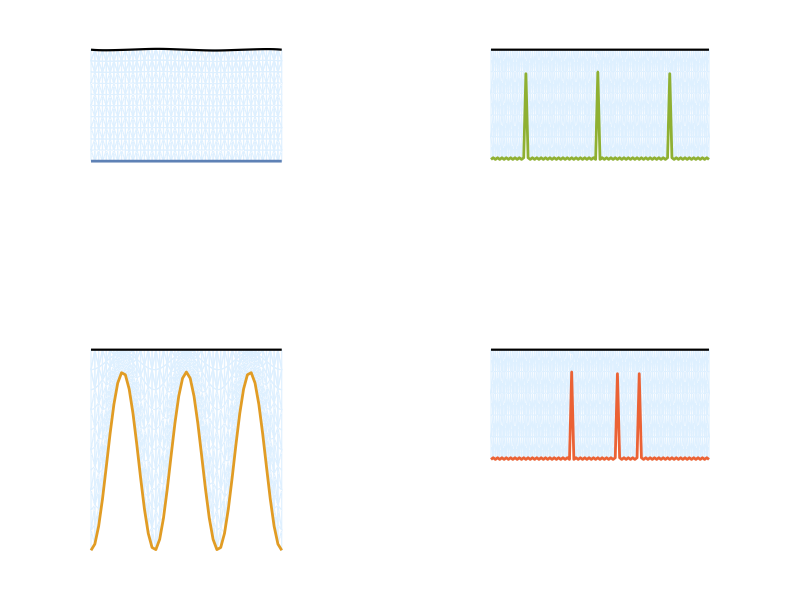
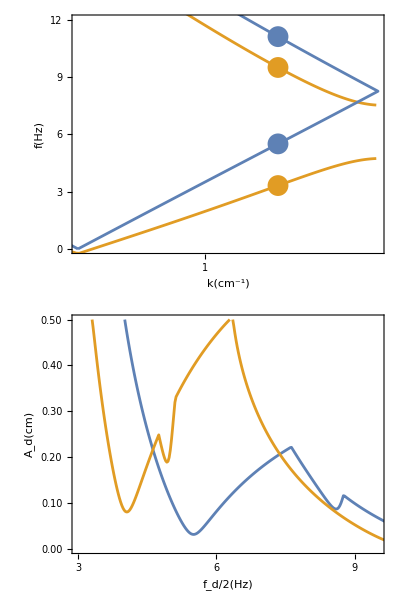
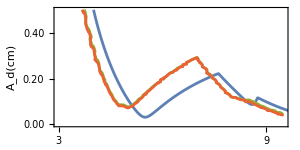
-Graphics- | -Graphics- | -Graphics- | -Graphics-

Export::nodir: Directory /Users/zack/Documents/oscillators/faraday/plots/ does not exist.

Export::noopen: Cannot open plots/sharpsubstrates.pdf.

$Failed

```mathematica
p=Grid[{{p0,Grid[{{Show[p1,AspectRatio->1/2]},{Show[p2,AspectRatio->1/2]}}],Show[p4,AspectRatio->1/2],Show[p3,AspectRatio->1/2]}}]
Export["plots/sharpsubstrates.pdf",p]
```

## Fig 4

```mathematica
Needs["ErrorBarPlots`"]
directory="data"
filebase="flat2";
data0=Import[directory<>"/"<>filebase<>"/"<>filebase<>".txt","Table"];filebase="periodic2";
data1=Import[directory<>"/"<>filebase<>"/"<>filebase<>".txt","Table"];
filebase="random2";
data2=Import[directory<>"/"<>filebase<>"/"<>filebase<>".txt","Table"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

data

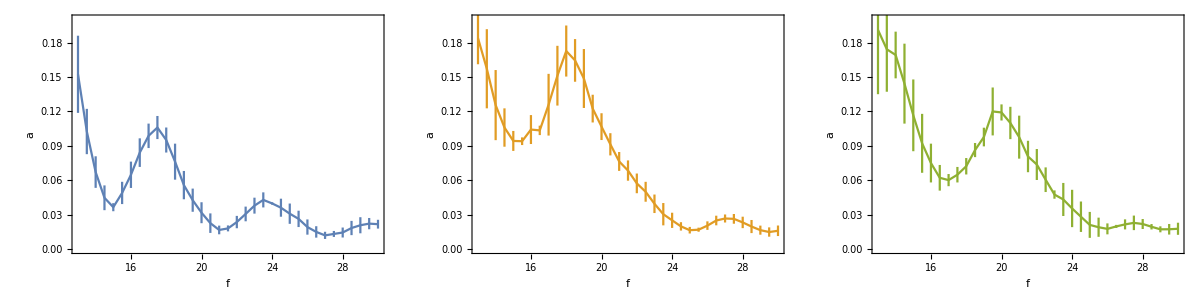

```mathematica
p0=ErrorListPlot[DeleteCases[#,{}]&/@{Table[{{freq,Mean[#[[All,2]]]},If[Length[#]>2,ErrorBar[StandardDeviation[#[[All,2]]]],ErrorBar[0]]}&@({#[[3]],#[[2]]/(2*Pi*#[[3]])^2*980}&/@Cases[data0,u_/;Abs[u[[3]]-freq]<0.25]),{freq,13,30,0.5}]},Axes->False,Frame->True,FrameLabel->{"f","a"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,PlotRange->{{13,30},{0,0.2}},Joined->True];
p1=ErrorListPlot[DeleteCases[#,{}]&/@Table[{{freq,Mean[#[[All,2]]]},If[Length[#]>2,ErrorBar[StandardDeviation[#[[All,2]]]],ErrorBar[0]]}&@({#[[3]],#[[2]]/(2*Pi*#[[3]])^2*980}&/@Cases[data1,u_/;Abs[u[[3]]-freq]<0.25]),{freq,13,30,0.5}],Axes->False,Frame->True,FrameLabel->{"f","a"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[2]],PlotRange->{{13,30},{0,0.2}},Joined->True];
p2=ErrorListPlot[DeleteCases[#,{}]&/@Table[{{freq,Mean[#[[All,2]]]},If[Length[#]>2,ErrorBar[StandardDeviation[#[[All,2]]]],ErrorBar[0]]}&@({#[[3]],#[[2]]/(2*Pi*#[[3]])^2*980}&/@Cases[data2,u_/;Abs[u[[3]]-freq]<0.25]),{freq,13,30,0.5}],Axes->False,Frame->True,FrameLabel->{"f","a"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,PlotStyle->ColorData[97,"ColorList"][[3]],PlotRange->{{13,30},{0,0.2}},Joined->True];
Grid[{{p0,p1,p2}}]
```

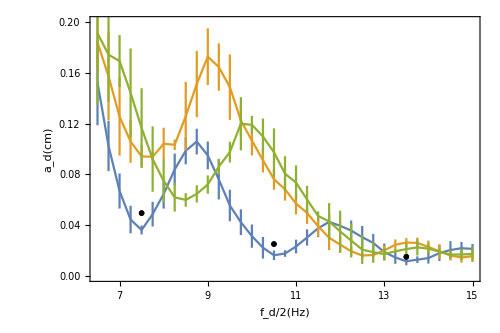

Export::nodir: Directory /Users/zack/Documents/oscillators/faraday/plots/ does not exist.

Export::noopen: Cannot open plots/combined.pdf.

$Failed

```mathematica
p=Show[p0,p1,p2,ListPlot[{{{15,0.45*980/(2*Pi*15)^2}},{{21,0.45*980/(2*Pi*21)^2}},{{27,0.45*980/(2*Pi*27)^2}}},PlotMarkers->"OpenMarkers",PlotStyle->Directive[Black,PointSize->0.04]],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.2,0.04}],Table[{i,""},{i,0,0.2,0.04}]},{Table[{i,i/2},{i,14,30,4}],Table[{i,""},{i,12,30,4}]}},FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[a,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},AspectRatio->2/3,ImageSize->500]
Export["plots/combined.pdf",p]
```

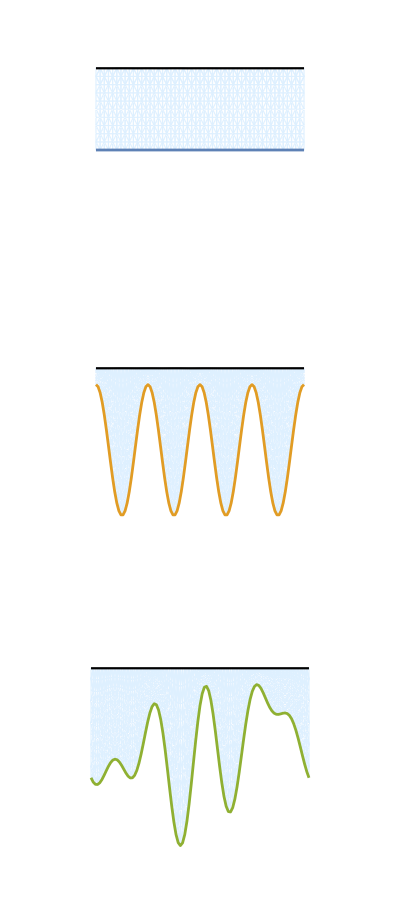

Export::nodir: Directory /Users/zack/Documents/oscillators/faraday/plots/ does not exist.

Export::noopen: Cannot open plots/substrates.pdf.

$Failed

```mathematica
filebase="data/flat";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=1;
mesh2=mesh[[m]];
p1=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black],Joined->True, ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}]];
filebase="data/periodic2";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=1;
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black],Joined->True, ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]]}]];
filebase="data/random";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=1;
mesh2=mesh[[m]];
p3=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], Joined->True,ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]]}]];

p0=Grid[{{p1},{p2},{p3}}]
Export["plots/substrates.pdf",p0]
```

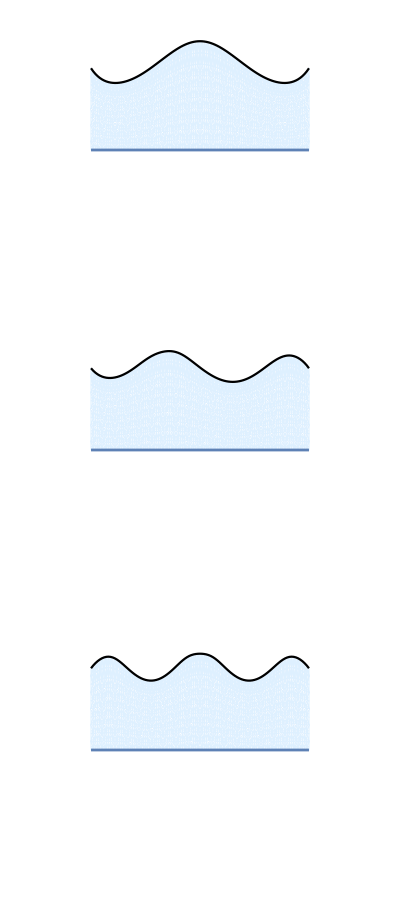

Export::nodir: Directory /Users/zack/Documents/oscillators/faraday/plots/ does not exist.

Export::noopen: Cannot open plots/modes.pdf.

$Failed

```mathematica
filebase="data/mode1";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-95;
mesh2=mesh[[m]];
p1=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black],Joined->True, ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}]];
filebase="data/mode2";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-87;
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black],Joined->True, ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}]];
filebase="data/mode3";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-100;
mesh2=mesh[[m]];
p3=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], Joined->True,ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}]];

p0=Grid[{{p1},{p2},{p3}}]
Export["plots/modes.pdf",p0]
```

#### Random substrates

Find the random substrate among 500 samples that maximizes the gap shifting of the tongues for the selected modes

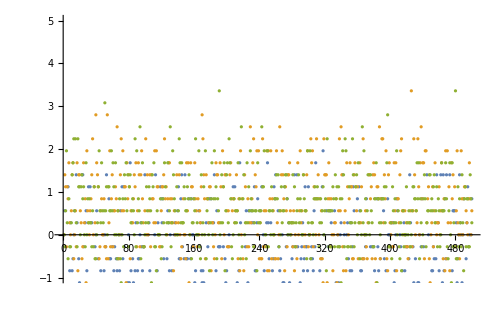

{480.,191.,51.,397.,218.,131.,94.,366.,243.,354.}

{426.,54.,170.,40.,229.,66.,438.,387.,340.,265.}

{229.,124.,299.,468.,142.,191.,131.,261.,244.,88.}

{4.2,3.36,6.44}

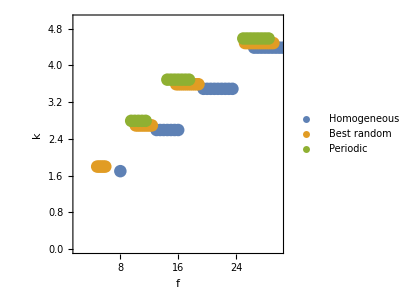

```mathematica
filebases={"sweeps/flat2acc","sweeps/periodic2acc"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,56}],1]&/@filebases;
filebase="sweeps/random";
random=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,500}],{}];
seeds=Flatten[DeleteDuplicates/@random[[All,All,7]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6]&/@random)[[All,All,5]]]]];
means[case_]:=Mean/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(means/@wavenumbers[[2;;4]])-(means/@wavenumbers[[1;;3]]);
mins[case_]:=Min/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
maxes[case_]:=Max/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(mins/@wavenumbers[[2;;-1]])-(maxes/@wavenumbers[[1;;-2]]);
shifts=Transpose[#-gaps[[All,1]]&/@(Transpose[gaps])];
ListPlot[shifts,ImageSize->500,PlotRange->{-1,5}]
DeleteCases[Reverse[SortBy[seeds,shifts[[3,First@FirstPosition[seeds,#]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]][[1;;10]]
DeleteCases[Reverse[SortBy[seeds,shifts[[2,First@FirstPosition[seeds,#]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]][[1;;10]]
DeleteCases[Reverse[SortBy[seeds,Mean[shifts[[2;;3,First@FirstPosition[seeds,#]]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]][[1;;10]]
m=191;
gaps[[All,m]]
minind=First@FirstPosition[Abs[DeleteDuplicates[sweeps[[1,All,2]]]-First@DeleteDuplicates[Flatten[random[[All,All,2]]]]],Min[Abs[DeleteDuplicates[sweeps[[1,All,2]]]-First@DeleteDuplicates[Flatten[random[[All,All,2]]]]]]];
min=DeleteDuplicates[sweeps[[1,All,2]]][[minind]];
ListPlot[{{#[[1]],#[[2]]-0.1}&/@Cases[sweeps[[1]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],Cases[random[[m]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.1}&/@Cases[sweeps[[2]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]]},PlotRange->{{2,30},{0,5}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"f","k"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]],AspectRatio->1,PlotStyle->Directive[PointSize[0.03]],PlotLegends->{"Homogeneous","Best random","Periodic"}]
```